```mathematica
Remove["Global`*"]
LordVader=Entity["PopularCurve", "DarthVaderCurve"];
DarthVaderCurve=EntityValue[LordVader,"ParametricEquations"];
f[t_]=DarthVaderCurve[t];
Productivity[30 "minutes"]=ParametricPlot[f[t],{t,π/2.8,π/1.5},Axes->False,Frame->True,FrameTicks->None,FrameLabel->{"Time","Productivity"}];
Productivity[2 "hours"]=ParametricPlot[f[t],{t,0,76π},Axes->False,Frame->True,FrameTicks->None,PlotStyle->{Thick,White},Background->Black,FrameLabel->{"Time","Productivity"},FrameStyle->White];
Noo=Import["~/Pictures/Luke Skywalker No.jpg","JPEG"];
text=-Graphics-;
```

## Analysis of productivity in Mathematica

### How I see my productivity at 30 minutes

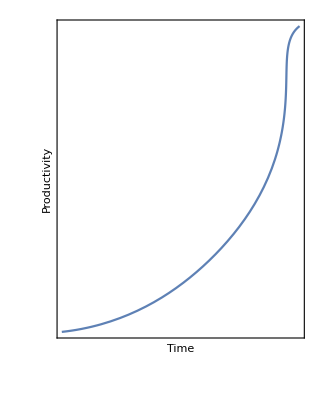

```mathematica
Print[Productivity[30 "minutes"]]
```

### ... 2 hours later

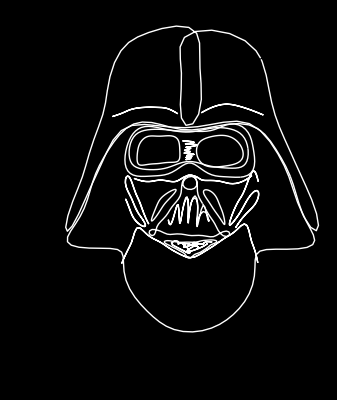

```mathematica
Print[Productivity[2 "hours"]]
```

(This is real mathematica code yo)

```mathematica
Print[Show[Noo,text,ImageSize->Medium]]
```

-Graphics-

```mathematica
ent=EntityClassList["PopularCurve"];
allcurves=EntityList/@ent;
```

```mathematica
{#,ent[[#]],g=Length[allcurves[[#]]];g}&/@Range[1,Length[ent]] //Grid[#,Spacings->{1, 1},Frame->None]&
```

1 | Mario curve | 9
2 | logo curve | 47
3 | shape curve | 48
4 | structure curve | 9
5 | food or drink curve | 14
6 | character curve | 8
7 | Disney curve | 12
8 | meme curve | 18
9 | person curve | 190
10 | plant curve | 8
11 | simple curve | 40
12 | animal curve | 105
13 | Family Guy curve | 4
14 | Futurama curve | 9
15 | Pokémon curve | 747
16 | Simpsons curve | 6
17 | SpongeBob SquarePants curve | 4
18 | Looney Tunes curve | 3
19 | closed curve | 48
20 | concave curve | 42
21 | Star Wars curve | 15
22 | music act curve | 9
23 | Avatar curve | 8
24 | fictional character curve | 2359
25 | musical instrument curve | 3
26 | League of Legends curve | 19
27 | DC Comics curve | 247
28 | person silhouette curve | 15
29 | vehicle curve | 13
30 | Pikmin curve | 5
31 | MS Paint Adventures curve | 11
32 | My Little Pony curve | 16
33 | Marvel Comics curve | 975

```mathematica
ins=allcurves[[21,14]];
dom=EntityValue[ins,"Domain"];
f[t_]=EntityValue[ins,"ParametricEquations"][t];
name=EntityValue[ins,"Name"];
```

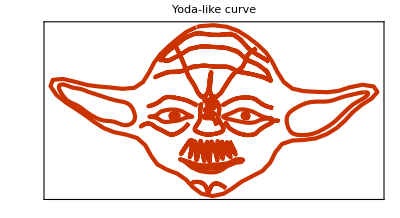

```mathematica
ParametricPlot[f[t],{t,dom[[1]],dom[[2]]},PlotLabel->name,PlotTheme->"Web",FrameTicks->None]
```

```mathematica
allcurves[[21]]
```

{Admiral Ackbar-like curve,C-3PO-like curve,Chewbacca-like curve,Darth Vader-like curve,Death Star-like curve,Han Solo-like curve,Jabba the Hutt-like curve,Jar Jar Binks-like curve,R2D2-like curve,Star Wars Alliance to Restore the Republic insignia-like curve,Star Wars Galactic Senate insignia-like curve,Star Wars Strategic Information Service insignia-like curve,X-wing-like curve,Yoda-like curve,Anakin Skywalker-like curve}